```mathematica
s={x'[t]== ((p[t]-q[t]*Cos[x[t]-y[t]])/(2-(Cos[x[t]-y[t]])^2)),
                    y'[t]==((2*q[t]-p[t]*Cos[x[t]-y[t]])/(2-(Cos[x[t]-y[t]])^2)),
p'[t]== -2Sin[x[t]]-((p[t]q[t]*Sin[x[t]-y[t]])/(2-(Cos[x[t]-y[t]])^2))+((((p[t])^2+2(q[t])^2-2p[t]q[t]*Cos[x[t]-y[t]])/(2*(2-(Cos[x[t]-y[t]])^2)^2))*Sin[2(x[t]-y[t])]),
q'[t]== -Sin[y[t]]+((p[t]q[t]*Sin[x[t]-y[t]])/(2-(Cos[x[t]-y[t]])^2))-((((p[t])^2+2(q[t])^2-2p[t]q[t]*Cos[x[t]-y[t]])/(2*(2-(Cos[x[t]-y[t]])^2)^2))*Sin[2(x[t]-y[t])])}

ics= {x[0]==Pi/6,y[0]==-Pi/3,p[0]==1,q[0]==-1}
sol=NDSolve[{s,ics},{x,y,p,q},{t,-200,200}]
Plot[Evaluate[x[t]/.sol],{t,-20,200}]
Plot[Evaluate[y[t]/.sol],{t,-20,200}]
Plot[Evaluate[p[t]/.sol],{t,-20,200}]
Plot[Evaluate[q[t]/.sol],{t,-20,200}]
ParametricPlot[Evaluate[{x[t],p[t]}/.sol],{t,-200,200}]
ParametricPlot[Evaluate[{y[t],q[t]}/.sol],{t,-200,200}]
```

{x'[t]==(-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] q[t]+{{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2),{{1,-1,-1},{0,1,-1},{0,0,1}}'[t]==(2 q[t]-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] {{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2),{{1,1,2},{0,1,1},{0,0,1}}'[t]==-2 Sin[x[t]]-(q[t] Sin[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] {{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)+(Sin[2 (x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t])] (2 q[t]^2-2 Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] q[t] {{1,1,2},{0,1,1},{0,0,1}}[t]+({{1,1,2},{0,1,1},{0,0,1}}[t])^2))/(2 (2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)^2),q'[t]==-Sin[{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]+(q[t] Sin[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] {{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)-(Sin[2 (x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t])] (2 q[t]^2-2 Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] q[t] {{1,1,2},{0,1,1},{0,0,1}}[t]+({{1,1,2},{0,1,1},{0,0,1}}[t])^2))/(2 (2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)^2)}

{x[0]==π/6,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3,{{1,1,2},{0,1,1},{0,0,1}}[0]==1,q[0]==-1}

NDSolve::ndode: The equations {{{1,1,2},{0,1,1},{0,0,1}}[0]==1,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3} are not differential equations or initial conditions in the dependent variables {q,x}.

NDSolve[{{x'[t]==(-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] q[t]+{{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2),{{1,-1,-1},{0,1,-1},{0,0,1}}'[t]==(2 q[t]-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] {{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2),{{1,1,2},{0,1,1},{0,0,1}}'[t]==-2 Sin[x[t]]-(q[t] Sin[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] {{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)+(Sin[2 (x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t])] (2 q[t]^2-2 Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] q[t] {{1,1,2},{0,1,1},{0,0,1}}[t]+({{1,1,2},{0,1,1},{0,0,1}}[t])^2))/(2 (2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)^2),q'[t]==-Sin[{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]+(q[t] Sin[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] {{1,1,2},{0,1,1},{0,0,1}}[t])/(2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)-(Sin[2 (x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t])] (2 q[t]^2-2 Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]] q[t] {{1,1,2},{0,1,1},{0,0,1}}[t]+({{1,1,2},{0,1,1},{0,0,1}}[t])^2))/(2 (2-Cos[x[t]-{{1,-1,-1},{0,1,-1},{0,0,1}}[t]]^2)^2)},{x[0]==π/6,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3,{{1,1,2},{0,1,1},{0,0,1}}[0]==1,q[0]==-1}},{x,{{1,-1,-1},{0,1,-1},{0,0,1}},{{1,1,2},{0,1,1},{0,0,1}},q},{t,-200,200}]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -15.5057 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndode: The equations {{{1,1,2},{0,1,1},{0,0,1}}[0]==1,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3} are not differential equations or initial conditions in the dependent variables {q,x}.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -15.5057 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndode: The equations {{{1,1,2},{0,1,1},{0,0,1}}[0]==1,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3} are not differential equations or initial conditions in the dependent variables {q,x}.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -15.5057 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndode: The equations {{{1,1,2},{0,1,1},{0,0,1}}[0]==1,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3} are not differential equations or initial conditions in the dependent variables {q,x}.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9955 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -15.5057 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndode: The equations {{{1,1,2},{0,1,1},{0,0,1}}[0]==1,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3} are not differential equations or initial conditions in the dependent variables {q,x}.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -199.992 cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -199.992 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{x'[-199.992]==(Times[«3»]+{«3»}[«1»])/Plus[«2»],{{«3»},{«3»},{«3»}}'[-199.992]==(Times[«2»]+Times[«3»])/Plus[«2»],{{«3»},{«3»},{«3»}}'[-199.992]==-2. Sin[«1»]-1. Power[«2»] q[«1»] Sin[«1»] {«3»}[«1»]+0.5 Power[«2»] Sin[«1»] Plus[«3»],q'[-199.992]==-1. Sin[«1»]+Power[«2»] q[«1»] Sin[«1»] {«3»}[«1»]-0.5 Power[«2»] Sin[«1»] Plus[«3»]},«1»},{x,{{1.,-1.,-1.},{0.,1.,-1.},{0.,0.,1.}},{{1.,1.,2.},{0.,1.,1.},{0.,0.,1.}},q},{-199.992,-200.,200.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -191.829 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndode: The equations {{{1,1,2},{0,1,1},{0,0,1}}[0]==1,{{1,-1,-1},{0,1,-1},{0,0,1}}[0]==-π/3} are not differential equations or initial conditions in the dependent variables {q,x}.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -199.992 cannot be used as a variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -199.992 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{x'[-199.992]==(Times[«3»]+{«3»}[«1»])/Plus[«2»],{{«3»},{«3»},{«3»}}'[-199.992]==(Times[«2»]+Times[«3»])/Plus[«2»],{{«3»},{«3»},{«3»}}'[-199.992]==-2. Sin[«1»]-1. Power[«2»] q[«1»] Sin[«1»] {«3»}[«1»]+0.5 Power[«2»] Sin[«1»] Plus[«3»],q'[-199.992]==-1. Sin[«1»]+Power[«2»] q[«1»] Sin[«1»] {«3»}[«1»]-0.5 Power[«2»] Sin[«1»] Plus[«3»]},«1»},{x,{{1.,-1.,-1.},{0.,1.,-1.},{0.,0.,1.}},{{1.,1.,2.},{0.,1.,1.},{0.,0.,1.}},q},{-199.992,-200.,200.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -191.829 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

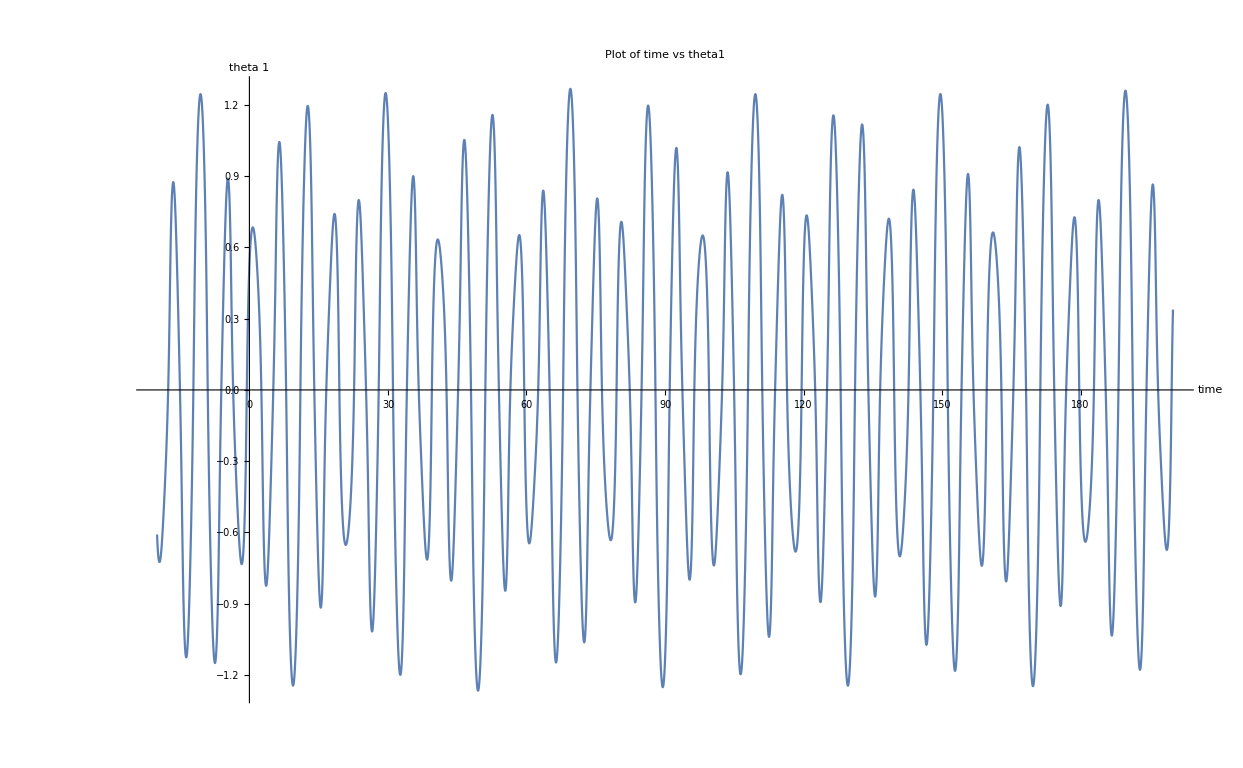

```mathematica
Show[%173,AxesLabel->{HoldForm[time],HoldForm[theta 1]},PlotLabel->HoldForm[Plot of time vs theta1],LabelStyle->{GrayLevel[0],Bold}]
```

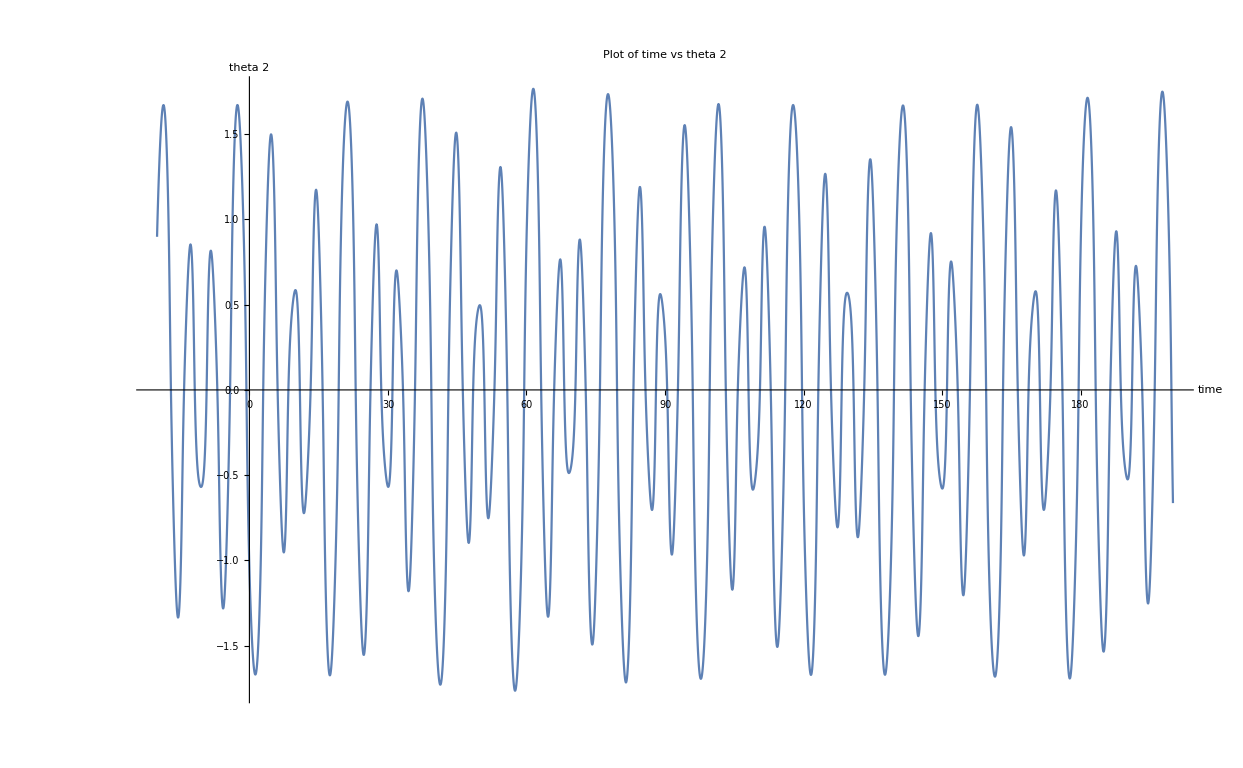

```mathematica
Show[%174,AxesLabel->{HoldForm[time],HoldForm[theta 2]},PlotLabel->HoldForm[Plot of time vs theta 2],LabelStyle->{GrayLevel[0],Bold}]
```

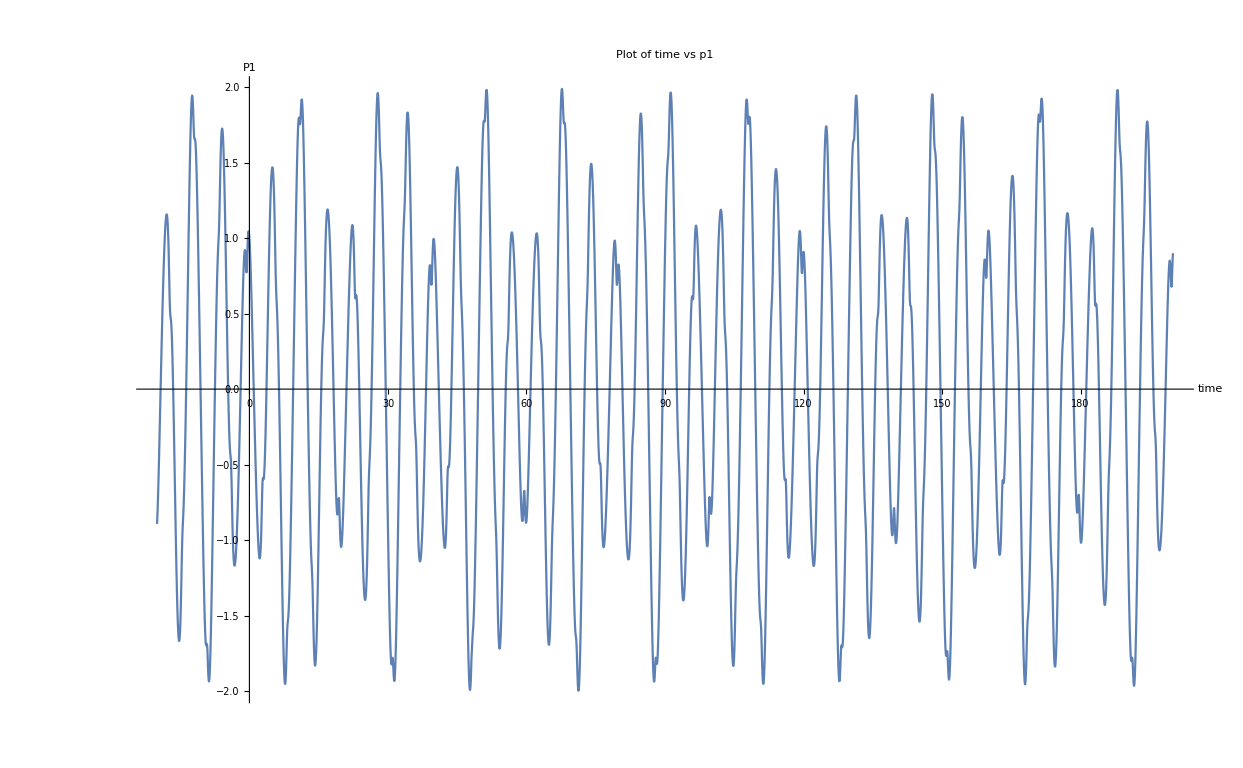

```mathematica
Show[%175,AxesLabel->{HoldForm[time],HoldForm[P1]},PlotLabel->HoldForm[Plot of time vs p1],LabelStyle->{GrayLevel[0],Bold}]
```

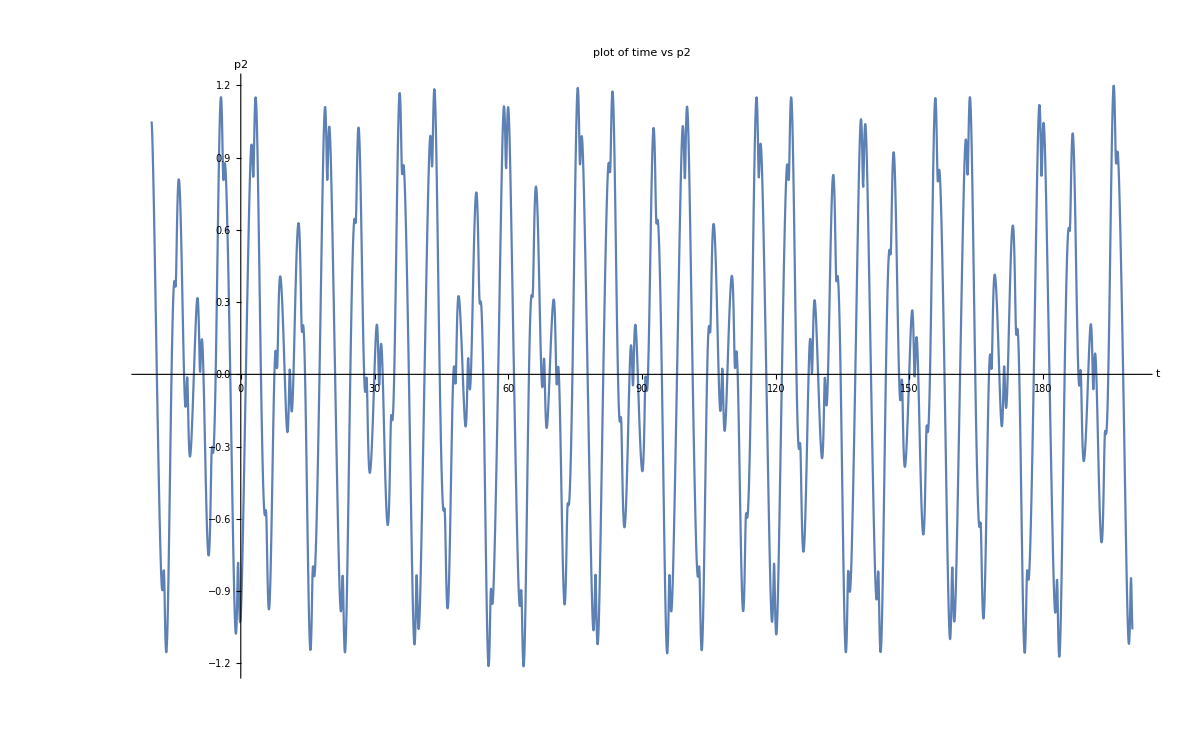

```mathematica
Show[%176,AxesLabel->{HoldForm[t],HoldForm[p2]},PlotLabel->HoldForm[plot of time vs p2],LabelStyle->{GrayLevel[0],Bold}]
```

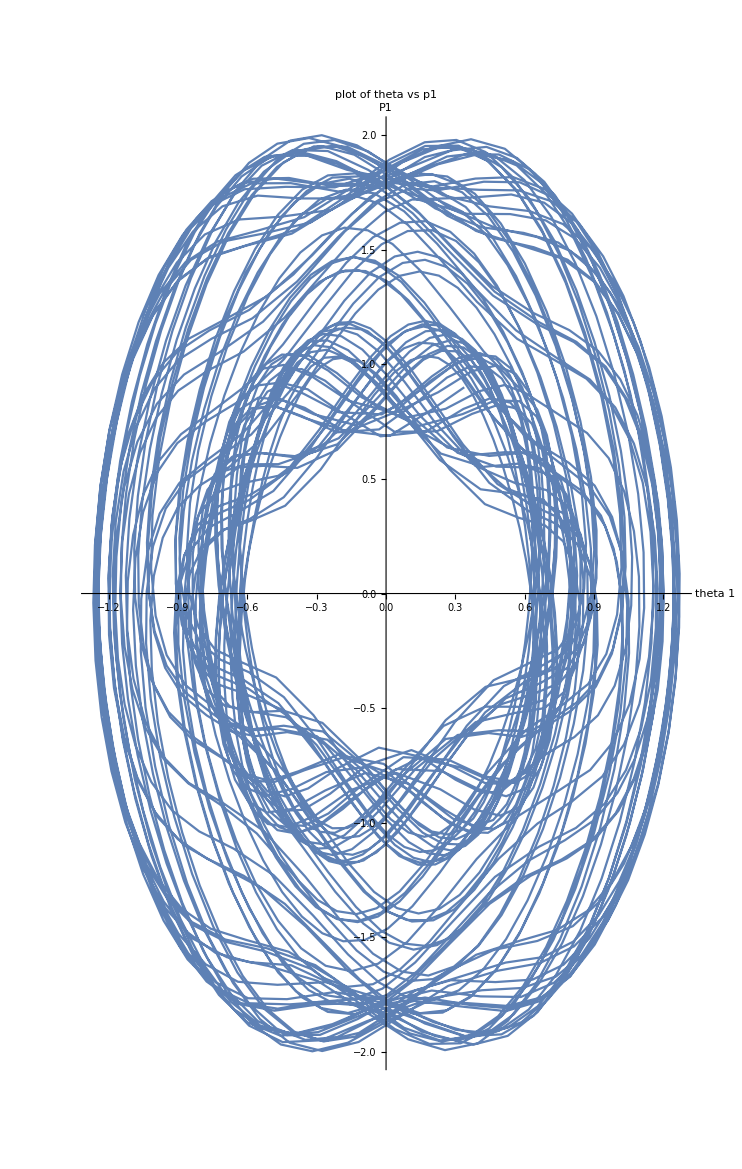

```mathematica
Show[%177,AxesLabel->{HoldForm[theta 1],HoldForm[P1]},PlotLabel->HoldForm[plot of theta vs p1],LabelStyle->{GrayLevel[0],Bold}]
```

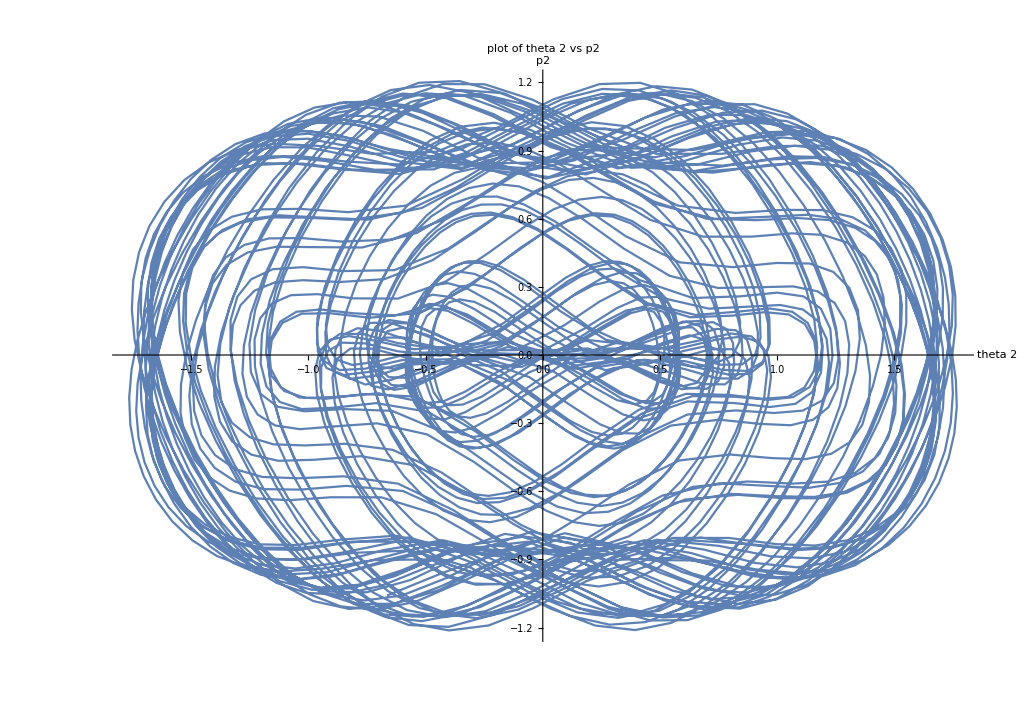

```mathematica
Show[%178,AxesLabel->{HoldForm[theta 2],HoldForm[p2]},PlotLabel->HoldForm[plot of theta 2 vs p2],LabelStyle->{GrayLevel[0]}]
```

```mathematica
3783.2015*1.21185-57.8304^2
```

```mathematica
1240.3175736150006
```

```mathematica
b={28.9799,10338257}
m=Inverse[{{1.21185,278410.327},{278410.327,139299716700}}]
m
m.b
```

{28.9799,10338257}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.21185,278410.},{278410.,1.393×10^11}} may contain significant numerical errors.

{{1.52577,-3.04947×10^-6},{-3.04947×10^-6,1.32736×10^-11}}

{{1.52577,-3.04947×10^-6},{-3.04947×10^-6,1.32736×10^-11}}

{12.6905,0.0000488522}

```mathematica
x={{1.21185,278410.327},{278410.327,139299716700}}
p={{1.5257687804647135,-3.049466252759235*10^-6},{-3.049466252759235*10^-6,1.327355819817086*10^-11}}
x.p
p.x
```

{{1.21185,278410.},{278410.,139299716700}}

{{1.52577,-3.04947×10^-6},{-3.04947×10^-6,1.32736×10^-11}}

{{1.,1.27055×10^-21},{5.82077×10^-11,1.}}

{{1.,5.82077×10^-11},{1.27055×10^-21,1.}}